# Universal Portfolio

The idea of the universal portfolio was introduced by information theorist Thomas Cover (1938-2012) in a 1991 paper. Interestingly, this isn’t the first time an information theorist brings a useful idea to the world of capital allocation, the first famous one being J. L. Kelly’s in his 1956 publication of “A New Interpretation of Information Rate”.

### The Universal Portfolio Beats the Market

The universal portfolio has caught the attention of many because of the statements that Cover made in the paper. A universal portfolio will, with high probability, beat the market portfolio  but more importantly beat a portfolio composed of the best performing stock. Stop and think about that for a minute: if you could look into the future, figure out what the best performing stock would be and make a portfolio composed only of that stock, a universal portfolio, without knowing about the future will, given enough time, beat the best-performing-stock portfolio. 

Everyone talks about how difficult it is to “beat the market”, and yet here comes an academic and tells us that the market can easily be beaten. You don’t even need to know much about the companies you’re investing in, just run this capital allocation program and you’re done. It seems to good to be true... besides, these academics and their fancy theories, if this was such a great idea, why didn’t Cover start a Universal Portfolio hedge fund?  Well it turns out that the ARA Group did recruit Cover for exactly this reason but the project was apparently stopped after Cover’s death in 2012.

If you are curious about the Universal Portfolio, this article is meant to give you a good understanding of the mathematics and the intuition behind Cover’s ideas. I’ve tried to explain every single concept as clearly as possible and assuming little background.

### Representing Stock Returns

Before I tell you about the intuition behind the Universal Portfolio, let me introduce an easy way of modelling stock returns and portfolios using Vectors. The idea is that there is a stock market with m stocks. The investor’s job is to allocate capital between the stocks. The way Cover modelled this is by representing the market using a sequence of vectors of returns r_1, r_2,..., r_n where r_i=(r_i1, r_i2,..., r_im) represents the returns of a single day.

Example
The following describe the returns of a market  composed of two stocks. So on the first day, stock one had a return of 1, meaning it didn’t change, while stock 2 had a return of 1.1, meaning a 10% increase. On the second day stock one increased by 5% while stock two increased by 20%, etc.

r_1=(1,1.1)
r_2=(1.05,1.2)
r_2=(0.8,0.9)

### Representing Allocations

We know that r_i represents the returns of the market on a given day, let’s talk about portfolios now. A portfolio is essentially a distribution of capital among options, so we can use a vector  p_i=(p_1,...,p_m) where p_i≥ 0 and ∑_(i=1)^m p_i=1. Such a vector p_i is called the portfolio vector and it describes the percentage to allocate to each stock.

Example:

p_1=(0.5,0.5)
p_2=(0.6,0.4)
p_2=(0.3,0.7)

p_1 is saying that we are allocating 50% of the portfolio to the first stock and 50% to the second stock. p_2 is saying 60% on the first and 40% on the second, etc.

### Why use vectors?

The reason we use vectors to represent stock returns and portfolios is that the product between two vectors produces the return of investing with a portfolio. Example:

p_1 r_1=0.5*1+0.5*1.1=1.05
p_2 r_2=0.6*1.05+0.4*1.2=1.11
p_3 r_3=0.30*0.8+0.7*0.9=0.87

And the net return, is just the following product:

∏_(i=1)^n p_i r_i

Which in our example is 1.05*1.11*0.87 = 1.01399

### Problem Statement

Let  W(p)=∏_(i=1)^n pr_i denote the wealth returned by investing with the same allocation percentages on every iteration and let  W_max=max_p  W(p)meaning W_max is the best returning constant portfolio.  We can think of W_max as the performance of an investor that knows the future, but must stick to a single allocation and never change his mind. Our goal will be to beat this investor.

The Universal Portfolio, on the other hand, will not know about the future, but we can change our allocation at any moment in time. The idea is that even without knowing the future, the Universal Portfolio can have a performance greater than W_max. 

The algorithm is actually quite simple: the i-th allocation p_i is the performance weighted average over all portfolios.

```mathematica
ConstantPortfolio[n_,portfolio_]:=Table[portfolio,{i,1,n}]

ReturnFactor[returns_, portfolio_]:= Product[
returns[[i]].portfolio,
{i,1,Length[returns]}
]

SplitIntoSequences[xs_]:=Table[Take[xs,i],{i,1,Length[xs]}]

ReturnFactorSequence[returns_, portfolios_]:=Block[{},
Assert[Length[returns]==Length[portfolios]];
FoldList[
Function[
{product, i},
product*(returns[[i]].portfolios[[i]])],
1,
Range[Length[returns]]]
]

GeneratePortfolios[2,{x_,y_}]:=Table[{i,1-i},{i,0,1,x}]

SumOverPortfolios[f_, portfolios_, deltaPortfolio_]:=Block[{},
Fold[
Function[
{sum,portfolio},
sum+f[portfolio]*deltaPortfolio
],
0,
portfolios
]
]

CalculateUniversalPortfolio[returns_]:=Block[{portfolios, deltaPortfolio},
deltaPortfolio={0.01,-0.01};
portfolios=GeneratePortfolios[2,deltaPortfolio];

SumOverPortfolios[#*ReturnFactor[returns,#]&,portfolios, deltaPortfolio]/SumOverPortfolios[ReturnFactor[returns,#]&, portfolios, deltaPortfolio]
]

SimulateUniversalPortfolioReturns[returns_]:=Block[{portfolios},
portfolios =SplitIntoSequences[returns]//
ParallelMap[CalculateUniversalPortfolio,#]&;
ReturnFactorSequence[returns, portfolios]
]

SimulateConstantPortfolioReturns[returns_,portfolio_]:=Block[{portfolios},
portfolios =ConstantPortfolio[Length[returns],portfolio];
ReturnFactorSequence[returns, portfolios]
]

ReturnVector[returnArrays_]:=
Table[
Table[returnArrays[[j]][[i]],{j,1,Length[returnArrays]}],
{i,1,Length[First[returnArrays]]}
]
```

```mathematica
range = {Today-Quantity[8,"Years"],Today}
symbol1="NYSE:SPY";
symbol2="NASDAQ:QQQ";
ge=FinancialData[symbol1,"Return",range]["Values"]//Map[#+1&];
aapl=FinancialData[symbol2,"Return",range]["Values"]//Map[#+1&];

{Length[ge],Length[aapl]}
```

{Day: Thu 6 Dec 2012,Day: Sun 6 Dec 2020}

{2010,2013}

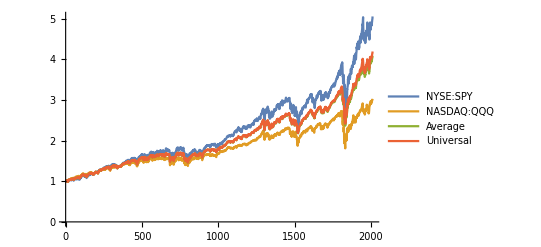

```mathematica
Block[{returnsVector, appleReturns,geReturns,averageReturns, universalReturns},
returnsVector=ReturnVector[{ge,aapl}];
appleReturns=SimulateConstantPortfolioReturns[returnsVector,{0,1}];
geReturns=SimulateConstantPortfolioReturns[returnsVector,{1,0}];
averageReturns=SimulateConstantPortfolioReturns[returnsVector,{0.5,0.5}];
universalReturns=SimulateUniversalPortfolioReturns[returnsVector];

ListPlot[
{appleReturns, geReturns,averageReturns, universalReturns},
PlotLegends->{symbol1,symbol2,"Average","Universal"},
Joined->True
]
]
```